```mathematica
EA=70000
EM=55000
as=75
af=150
es=as/EM
ef=0.04
aas=1.5 af
eas=aas/EA
```

70000

55000

75

150

3/2200

0.04

225.

0.00321429

```mathematica
Kt=40
thetamax=47.7/180*Pi
alphap1=60/180*Pi
r=3
Dsma=0.5
S=1/4 Pi Dsma^2
l0=100
alphae0=0/180*Pi
```

40

0.832522

π/3

3

0.5

0.19635

100

0

```mathematica
theta=p thetamax
alphap0=alphap1-thetamax
alpha=theta+alphap0
eps=r/l0(alpha-alphae0)
SigM[eps_]=Which[eps<es,EM eps,eps<ef,(af-as)/(ef-es)(eps-es)+as,eps≥ef,EM(eps-ef)+af]
SigA[eps_]=Which[eps<eas,EA eps]
TM=SigM[eps] S r
TA=SigA[eps] S r
```

0.832522 p

0.214675

0.214675+0.832522 p

3/100 (0.214675+0.832522 p)

Which[3/100 (0.214675+0.832522 p)<3/2200,EM eps,eps<ef,((af-as) (eps-es))/(ef-es)+as,eps≥ef,EM (eps-ef)+af]

Which[3/100 (0.214675+0.832522 p)<0.00321429,EA eps]

0.589049 Which[3/100 (0.214675+0.832522 p)<3/2200,1/100 EM (3 (0.214675+0.832522 p)),3/100 (0.214675+0.832522 p)<ef,((af-as) (3/100 (0.214675+0.832522 p)-es))/(ef-es)+as,3/100 (0.214675+0.832522 p)≥ef,EM (3/100 (0.214675+0.832522 p)-ef)+af]

0.589049 Which[3/100 (0.214675+0.832522 p)<0.00321429,1/100 EA (3 (0.214675+0.832522 p))]

```mathematica
data1=Import["C:\\Users\\surralyn\\OneDrive - buaa.edu.cn\\文档\\mathematica\\1.csv","CSV"]
data2=Import["C:\\Users\\surralyn\\OneDrive - buaa.edu.cn\\文档\\mathematica\\2.csv","CSV"]
data3=Import["C:\\Users\\surralyn\\OneDrive - buaa.edu.cn\\文档\\mathematica\\3.csv","CSV"]
weight1=Fit[data1,{1,p,p^2},p]
weight2=Fit[data2,{1,p,p^2},p]
weight3=Fit[data3,{1,p,p^2},p]
```

CreatePaclet::badppi: The paclet C:\Users\surralyn\AppData\Roaming\Mathematica\Paclets\Temporary\CloudObject-12.1.1424009.paclet does not have a properly formatted PacletInfo.m or PacletInfo.wl file. You can use the VerifyPaclet function to get more detailed information about the error.

PacletInstall::instl: An error occurred installing paclet from file C:\Users\surralyn\AppData\Roaming\Mathematica\Paclets\Temporary\CloudObject-12.1.1424009.paclet: Not a valid paclet.

{{0,13.8},{0.0001,13.8},{0.0002,13.9},{0.00029979,13.9},{0.000400419,13.9},{0.000501048,13.9},{0.000599581,13.9},{0.00070021,13.9},{0.000800839,13.9},{0.000899371,13.9},{0.001,13.9},{0.00110063,13.9},{0.00119916,13.9},{0.00129979,13.9},{0.00140042,13.9},{0.00150105,13.9},{0.00159958,13.9},9967,{0.997904,25.5},{0.997904,25.5},{0.997904,25.5},{0.997904,25.5},{0.997904,25.5},{0.997904,25.5},{1,25.5},{1,25.5},{1,25.5},{1,25.5},{1,25.5},{1,25.5},{1,25.5},{1,25.5},{1,25.5},{1,25.5},{1,25.5}}
 |  |  |  |

{{0,16.6},{0.0001,16.6},{0.0002,16.6},{0.00029979,16.6},{0.000400419,16.6},{0.000501048,16.6},{0.000599581,16.6},{0.00070021,16.6},{0.000800839,16.6},{0.000899371,16.6},{0.001,16.6},{0.00110063,16.6},{0.00119916,16.6},{0.00129979,16.6},{0.00140042,16.6},{0.00150105,16.6},{0.00159958,16.6},9967,{0.997904,30.8},{0.997904,30.8},{0.997904,30.8},{0.997904,30.8},{0.997904,30.8},{0.997904,30.8},{1,30.8},{1,30.8},{1,30.8},{1,30.8},{1,30.8},{1,30.8},{1,30.8},{1,30.8},{1,30.8},{1,30.8},{1,30.8}}
 |  |  |  |

{{0,11.1},{0.0001,11.1},{0.0002,11.1},{0.00029979,11.1},{0.000400419,11.1},{0.000501048,11.1},{0.000599581,11.1},{0.00070021,11.1},{0.000800839,11.1},{0.000899371,11.1},{0.001,11.1},{0.00110063,11.1},{0.00119916,11.1},{0.00129979,11.1},{0.00140042,11.1},{0.00150105,11.1},{0.00159958,11.1},9967,{0.997904,20.4},{0.997904,20.4},{0.997904,20.4},{0.997904,20.4},{0.997904,20.4},{0.997904,20.4},{1,20.4},{1,20.4},{1,20.4},{1,20.4},{1,20.4},{1,20.4},{1,20.4},{1,20.4},{1,20.4},{1,20.4},{1,20.4}}
 |  |  |  |

13.7732+19.1571 p-7.35975 p^2

16.505+23.2376 p-8.8664 p^2

11.0211+15.3304 p-5.88982 p^2

```mathematica
flow1={{0.0,174.842636},{0.2,161.5433058},{0.4,141.0133919},{0.6,96.09668112},{0.8,35.00371777},{1.0,5.717576773}}
flow2={{0.0,214.8836829},{0.2,184.9972781},{0.4,159.3328299},{0.6,127.0373705},{0.8,70.71259988},{1.0,3.165048405}}
flow3={{0.0,174.8361333},{0.2,161.6325707},{0.4,141.1477518},{0.6,95.95649634},{0.8,39.06853732},{1.0,-4.534971439}}
flowF1=Fit[flow1,{1,p,p^2},p]
flowF2=Fit[flow2,{1,p,p^2},p]
flowF3=Fit[flow3,{1,p,p^2},p]
```

{{0.,174.843},{0.2,161.543},{0.4,141.013},{0.6,96.0967},{0.8,35.0037},{1.,5.71758}}

{{0.,214.884},{0.2,184.997},{0.4,159.333},{0.6,127.037},{0.8,70.7126},{1.,3.16505}}

{{0.,174.836},{0.2,161.633},{0.4,141.148},{0.6,95.9565},{0.8,39.0685},{1.,-4.53497}}

178.679-73.3327 p-108.119 p^2

210.59-66.0047 p-138.816 p^2

177.189-54.2429 p-132.863 p^2

```mathematica
switchstring=1
switchweight=0
switchflow=0
TO1=Kt(Pi-alpha)*switchstring-weight1*switchweight+flowF1*switchflow
TO2=Kt(Pi-alpha)*switchstring-weight2*switchweight+flowF2*switchflow
TO3=Kt(Pi-alpha)*switchstring-weight3*switchweight+flowF3*switchflow
```

1

0

0

40 (2.92692-0.832522 p)

40 (2.92692-0.832522 p)

40 (2.92692-0.832522 p)

```mathematica
40 (2.9269171555944906-0.8325220532012952 th/thetamax)
```

40 (2.92692-1. th)

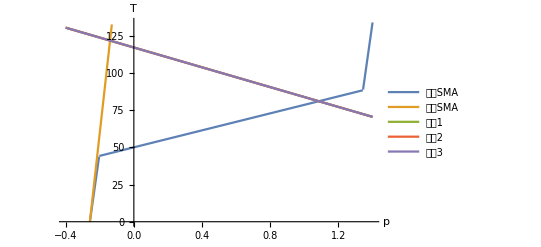

```mathematica
Plot[{TM,TA,TO1,TO2,TO3},{p,-0.4,1.4},AxesLabel->{p,T},PlotLegends->{"低温SMA","高温SMA","阀门1","阀门2","阀门3"}]
```

40 (2.92692-0.832522 p)

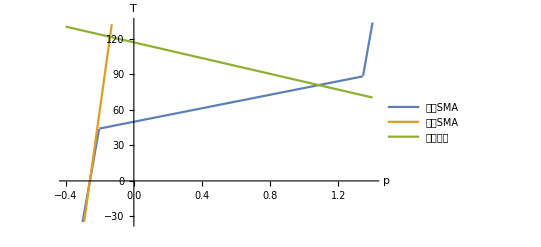

```mathematica
TO=Kt(Pi-alpha)
Plot[{TM,TA,TO},{p,-0.4,1.4},AxesLabel->{p,T},PlotLegends->{"低温SMA","高温SMA","偏置弹簧"}]
```

```mathematica
SigMcal[eps_]=(af-as)/(ef-es)(eps-es)+as
SigAcal[eps_]=EA eps
TMcal=SigMcal[eps] S r
TAcal=SigAcal[eps] S r
```

75+1941.18 (-3/2200+3/100 (0.214675+0.832522 p))

2100 (0.214675+0.832522 p)

0.589049 (75+1941.18 (-3/2200+3/100 (0.214675+0.832522 p)))

1237. (0.214675+0.832522 p)

```mathematica
Solve[TMcal==TO1,p]
```

{{p→-2.46569},{p→0.933824}}

```mathematica
Solve[TAcal==TO1,p]
```

{{p→-11.4834},{p→0.014199}}

```mathematica
Remove["Global`*"]
```

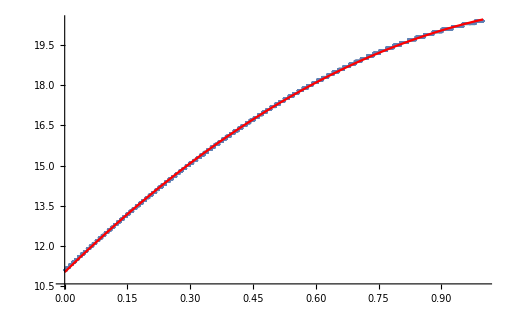

```mathematica
Show[ListPlot[data3],Plot[line3,{x,0,1},PlotStyle->Red]]
```

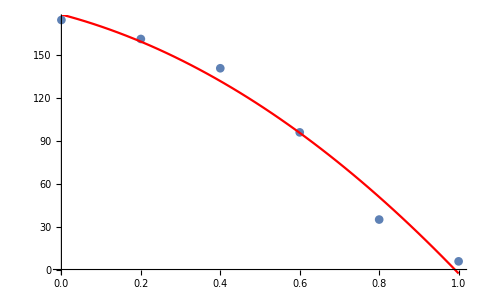

```mathematica
Show[ListPlot[flow1],Plot[flowF1,{p,0,1},PlotStyle->Red]]
```

```mathematica
TM
```

0.589049 Which[3/100 (0.214675+0.832522 p)<3/2200,1/100 EM (3 (0.214675+0.832522 p)),3/100 (0.214675+0.832522 p)<ef,((af-as) (3/100 (0.214675+0.832522 p)-es))/(ef-es)+as,3/100 (0.214675+0.832522 p)≥ef,EM (3/100 (0.214675+0.832522 p)-ef)+af]

```mathematica
Simplify[0.5890486225480862((af-as) (3/100 (0.2146754979953024+0.8325220532012952 al/47.7)-es))/(ef-es)+as]
```

80.8049+0.598708 al

```mathematica
80.80485737120023/0.5987076199190237
```

134.965

```mathematica
208.6496055417796+16.963382564372335 47.7
```

1017.8

```mathematica
Simplify[40 (2.9269171555944906-0.8325220532012952 al/47.7)]
```

117.077-0.698132 al

```mathematica
117.07668622377963/0.6981317007977318
```

167.7

```mathematica
a=(p r)/(p + r-p r)
prin = 4a + p+4 r
Plot3D[prin,{p,0,1},{r,0,1}]
```

(p r)/(p+r-p r)

p+4 r+(4 p r)/(p+r-p r)

-Graphics3D-